Nonterminals to search for.

```mathematica
gpatFunctions={plus,times,atan,sin, gauss};
(*gpFunctions={abs,plus,minus,times,div,mod,atan,cos,sin, gauss,gaussdif};*)
gpFunctions={plus,times,atan,sin, gauss};
```

Read the best so far genome. Returns expression.

```mathematica
readBSFGenome[fileName_]:= 
Module[{str,line,prev},
(*ToExpression[StringSplit[Import[fileName],"\n"]]⟦-1,1,1⟧;*)
str=OpenRead[fileName];
line=Read[str, String];
While[line=!=EndOfFile,prev=line;line=Read[str, String]];
Sequence@@ToExpression[prev]⟦1⟧
]
```

Computes the ratio of the amount of each type of nonterminal.

```mathematica
computeFunctionRatios[genome_, functions_]:=
Module[{counts,total},
counts=Length[Position[genome,#]]&/@functions;
total=Total[counts];
If[total==0,counts,counts/total]
]
```

Computes average ratio from all experiments in a directory.

```mathematica
computeAverageFunctionRatios[dir_,functions_]:=
Module[{},
Mean[computeFunctionRatios[readBSFGenome[#],functions]&/@FileNames["*O_GENOMES_MATH.txt",dir]]
]
```

Plot it as a bar chart.

```mathematica
plotAverageFunctionRatios[dir_,functions_]:=BarChart[computeAverageFunctionRatios[dir,functions],ChartStyle->"Rainbow",ChartLegends->functions]
```

```mathematica
computeFunctionRatios[bsfGenome,gpatFunctions]
```

{1/5,2/5,1/5,0,1/5}

```mathematica
avgRatios=computeAverageFunctionRatios["~/java/exp/GPAT/",gpatFunctions]
```

{71/250,737/1500,29/500,1/30,2/15}

```mathematica
List/@avgRatios
```

{{71/250},{737/1500},{29/500},{1/30},{2/15}}

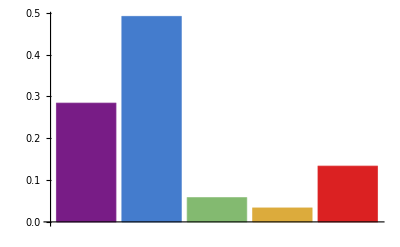
-Graphics--Graphics- | plus
-Graphics- | times
-Graphics- | atan
-Graphics- | sin
-Graphics- | gauss

```mathematica
plotAverageFunctionRatios["~/java/exp/GPAT/",gpatFunctions]
```

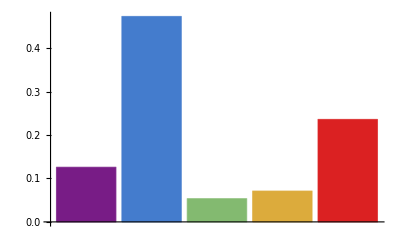
-Graphics--Graphics- | plus
-Graphics- | times
-Graphics- | atan
-Graphics- | sin
-Graphics- | gauss

```mathematica
plotAverageFunctionRatios["~/java/exp/GP/",gpFunctions]
```